```mathematica
$Path
```

{C:\Program Files\java-neon\eclipse\..\..\..\Users\fabregas.TCMM\.p2\pool\plugins\com.wolfram.eclipse.MEET_10.1.757\MathematicaSourceVersioned\Head,C:\Program Files\java-neon\eclipse\..\..\..\Users\fabregas.TCMM\.p2\pool\plugins\com.wolfram.eclipse.MEET_10.1.757\MathematicaSource,C:\Users\fabregas.TCMM\.eclipse\org.eclipse.platform_4.6.1_1487748986_win32_win32_x86_64\configuration\org.eclipse.osgi\477\0\.cp\MathematicaSource,C:/Users/fabregas.TCMM/Google Drive/Borsa/Borsa mat/Workspace/Borsa/BorsaV0/Borsa,C:/Users/fabregas.TCMM/Google Drive/Borsa/Borsa mat/Workspace/Borsa/BorsaV0,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links,C:\Users\fabregas.TCMM\AppData\Roaming\Mathematica\Kernel,C:\Users\fabregas.TCMM\AppData\Roaming\Mathematica\Autoload,C:\Users\fabregas.TCMM\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\fabregas.TCMM,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\10.4\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Data\ICC}

```mathematica
?EmbeddingAnalysis`*
```

```mathematica
Ticker={"ABE.MC","ACS.MC","ACX.MC","AENA.MC","AMS.MC","ANA.MC","BBVA.MC","BKIA.MC","BKT.MC","CABK.MC","CLNX.MC","DIA.MC","ELE.MC","ENG.MC","FCC.MC","FER.MC","GAM.MC","GAS.MC","GRF.MC","IAG.MC","IBE.MC","IDR.MC","ITX.MC","MAP.MC","MRL.MC","MTS.MC","POP.MC","REE.MC","REP.MC","SAB.MC","SAN.MC","TEF.MC","TL5.MC","TRE.MC","VIS.MC"}
```

{ABE.MC,ACS.MC,ACX.MC,AENA.MC,AMS.MC,ANA.MC,BBVA.MC,BKIA.MC,BKT.MC,CABK.MC,CLNX.MC,DIA.MC,ELE.MC,ENG.MC,FCC.MC,FER.MC,GAM.MC,GAS.MC,GRF.MC,IAG.MC,IBE.MC,IDR.MC,ITX.MC,MAP.MC,MRL.MC,MTS.MC,POP.MC,REE.MC,REP.MC,SAB.MC,SAN.MC,TEF.MC,TL5.MC,TRE.MC,VIS.MC}

```mathematica
Put[Ticker,"C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Ticker\\Ticker"]
```

```mathematica
Ticker=Get["C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Ticker\\Ticker"]
```

{ABE.MC,ACS.MC,ACX.MC,AENA.MC,AMS.MC,ANA.MC,BBVA.MC,BKIA.MC,BKT.MC,CABK.MC,CLNX.MC,DIA.MC,ELE.MC,ENG.MC,FCC.MC,FER.MC,GAM.MC,GAS.MC,GRF.MC,IAG.MC,IBE.MC,IDR.MC,ITX.MC,MAP.MC,MRL.MC,MTS.MC,POP.MC,REE.MC,REP.MC,SAB.MC,SAN.MC,TEF.MC,TL5.MC,TRE.MC,VIS.MC}

```mathematica
ibex35=Get["C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Ticker\\"<>#]&/@Ticker;
```

```mathematica
ams=ibex35[[5]]
```

AMS.MC
from  Thu 29 Apr 2010  to  Wed 14 Dec 2016
1726  barsStock Object

```mathematica
cs=ams["Close"][[800;;-1,2]];
```

```mathematica
rm=recurrenceMatrix[cs,1,20,0.5,900];
```

```mathematica
ArrayPlot[rm]
```

-Graphics-

```mathematica
sp60=kNNForecast[cs,20,120,3];
```

```mathematica
Length[sp60]
```

1047

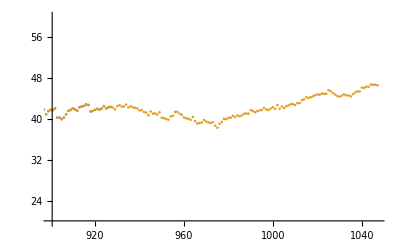

```mathematica
ListPlot[{ams["Close"][[800;;,2]],sp60},PlotRange->{{900,1047},{20,60}}]
```

```mathematica
phasePortrait3DManipulation[cs]
```

```mathematica
phasePortraitManipulation[cs]
```

```mathematica
entropyH[cs]
```

2.81806

```mathematica
entropyH[cs[[1;;2980]],cs[[21;;3000]]]
```

4.40602

```mathematica
mutualInformationH[cs[[1;;2980]],cs[[21;;3000]]]
```

1.21905

```mathematica
distanceMutualInformationH[cs[[1;;2980]],cs[[21;;3000]]]
```

0.723322

```mathematica
X=Transpose@MovingMap[Identity,cs,499];
```

```mathematica
Length/@X
```

{2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902,2902}

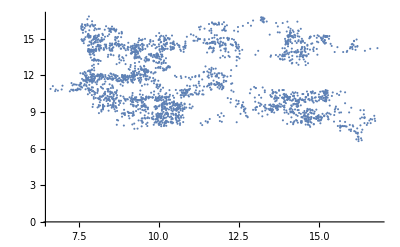

```mathematica
ListPlot[Transpose@{X[[1]],X[[500]]}]
```

```mathematica
mi=mutualInformationH[X[[1]],X[[#]]]&/@Range[1,500];
```

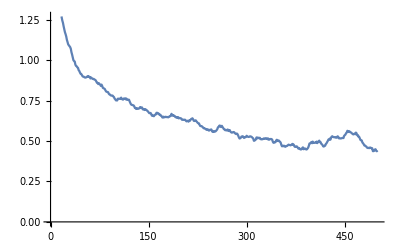

```mathematica
ListLinePlot[mi]
```

```mathematica
dmi=distanceMutualInformationH[X[[1]],X[[#]]]&/@Range[1,500];
```

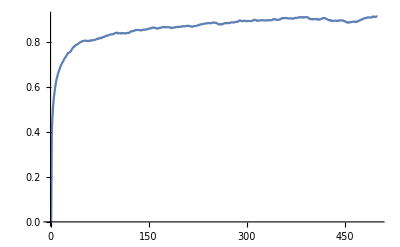

```mathematica
ListLinePlot[dmi]
```

```mathematica
falseNearestNeighbors[cs,50,10,15,2]
```

{{1,0.493731},{2,0.399862},{3,0.0606805},{4,0.00321314},{5,0.000727008},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.}}

```mathematica
tab=Table[{i,3,1},{i,1,49}]
```

{{1,3,1},{2,3,1},{3,3,1},{4,3,1},{5,3,1},{6,3,1},{7,3,1},{8,3,1},{9,3,1},{10,3,1},{11,3,1},{12,3,1},{13,3,1},{14,3,1},{15,3,1},{16,3,1},{17,3,1},{18,3,1},{19,3,1},{20,3,1},{21,3,1},{22,3,1},{23,3,1},{24,3,1},{25,3,1},{26,3,1},{27,3,1},{28,3,1},{29,3,1},{30,3,1},{31,3,1},{32,3,1},{33,3,1},{34,3,1},{35,3,1},{36,3,1},{37,3,1},{38,3,1},{39,3,1},{40,3,1},{41,3,1},{42,3,1},{43,3,1},{44,3,1},{45,3,1},{46,3,1},{47,3,1},{48,3,1},{49,3,1}}

```mathematica
pred=TStepPrediction[cs[[1;;-50]],49,1,tab] (* ????? *)
```

{15.1047,15.069,15.1952,15.048,15.1999,15.1413,15.1229,14.9456,15.2325,15.252,15.0467,14.9873,14.7282,14.7086,14.6888,14.7222,14.7157,14.3769,14.1576,14.0182,14.3572,14.3307,14.4172,14.4372,14.4904,14.4905,14.4839,14.4573,14.3443,14.1316,14.2447,14.1915,14.2248,14.0985,14.0985,14.3577,14.4242,14.3445,14.3245,14.1983,14.2515,14.0321,14.0121,14.1783,14.1251,14.0653,14.0188,14.1584,14.2515}

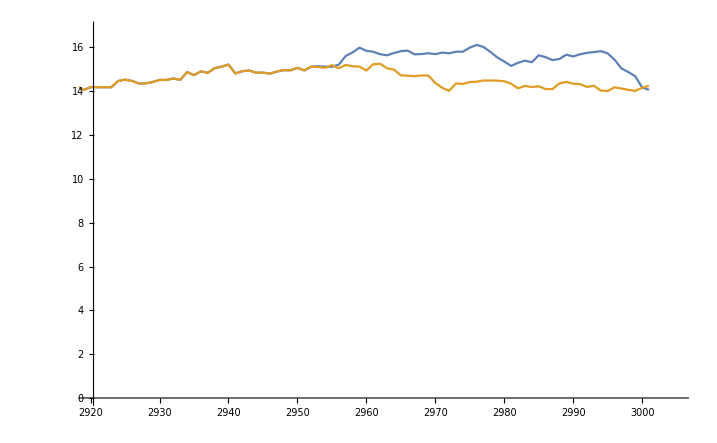

```mathematica
ListLinePlot[{cs,Join[cs[[1;;-50]],pred]},PlotRange->{{2920,3005},Automatic}]
```

```mathematica
ssa=singularSpectrumAnalysis[cs[[-1500;;]],250,25];
```

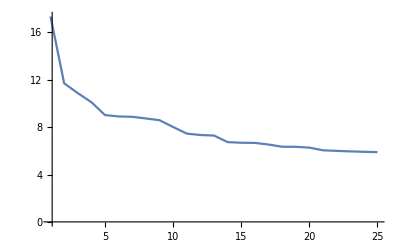

```mathematica
ssaPlotEigenvalues[ssa,25]
```

```mathematica
entropy=-ssa[[1]]/Plus@@ssa[[1]] Log[ssa[[1]]/Plus@@ssa[[1]]];
```

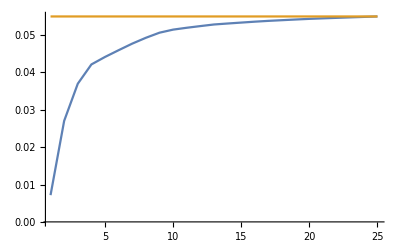

```mathematica
ListLinePlot[{Accumulate[entropy],Table[Plus@@entropy,Length[entropy]]},PlotRange->All]
```

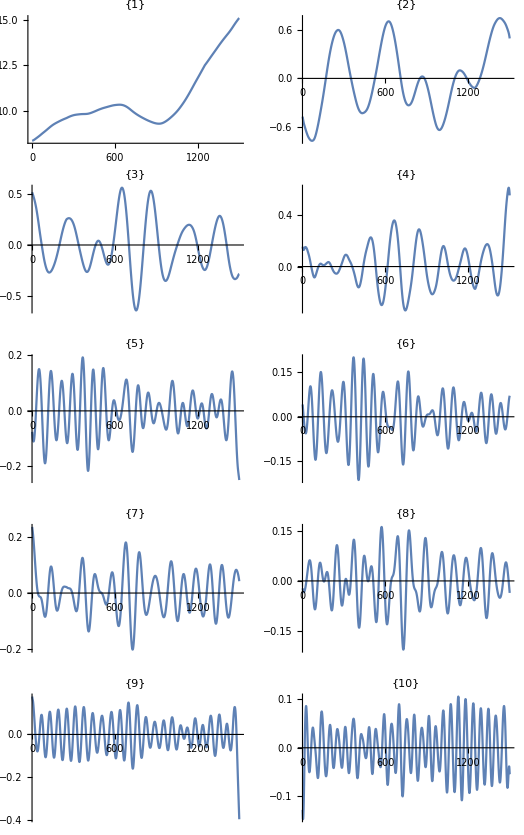

```mathematica
ssaPlotComponents[ssa,10]
```

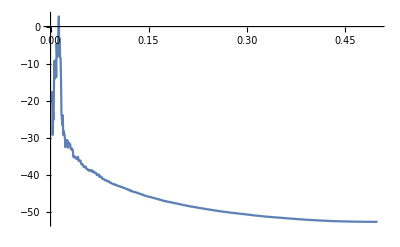

```mathematica
Periodogram[ssa[[2,5]],PlotRange->All]
```

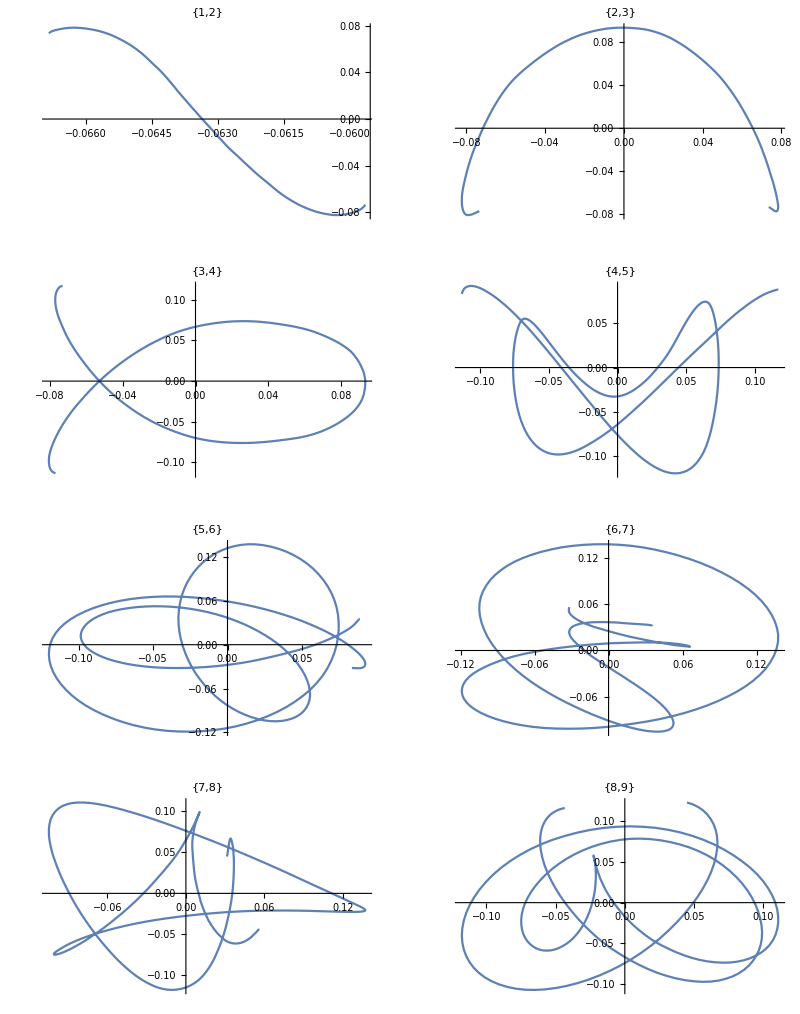

```mathematica
ssaPlotPairVectors[ssa,10]
```

```mathematica
ssawCorrelation[ssa,25]
```

-Graphics-

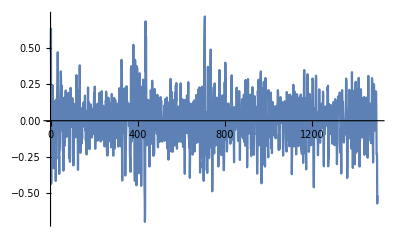

```mathematica
ssaPlotResiduals[ssa,cs[[-1500;;]],25]
```

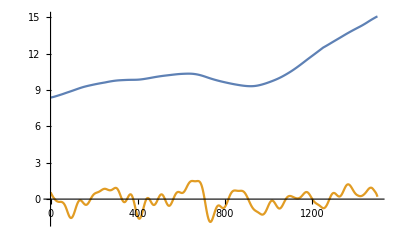

```mathematica
ListLinePlot[{ssaSmoothing[ssa,1],ssaSmoothing[ssa,{2,3,4,5,6,7,8,9}]}]
```

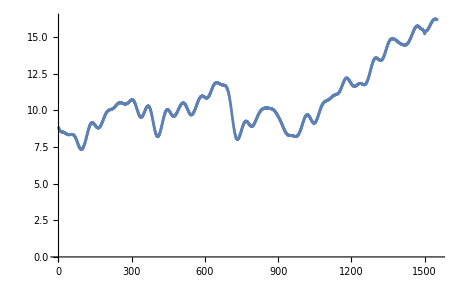

```mathematica
ListPlot[ssaRForecasting[ssa,10,50]]
```

```mathematica
?Borsa`*
```

```mathematica
?Stock`*
```